```mathematica
(* Putting in required known constants *)
(*M = 1.2209*10^19 ;*)(* Non-reduced Planck Mass in GeV/c^2 *)
(*M = 1*)
δ = 4.5*10^-5 ;(*I think this is the current value I'm using*)
```

```mathematica
(* Potential, without normalization *)
V[θ_] = θ^4; (* θ is ϕ/M *)

(* Slow-roll parameters *)
(*H[θ_]=√((8 π)/(3 M^2)V[θ]);*)
ϵ[ϕ_] = 1/(16 π)(V'[ϕ]/V[ϕ])^2;
(* Field Value at the end of inflation *)
θe = Re[x/. FindRoot[ϵ[x]==1,{x,1}]]
Nume[θ_?NumberQ]:=Re[(8 π) NIntegrate[V[x]/V'[x],{x, θe,θ}]]

(* Field value NN e-folds before the end of inflation. Exact answer: *)
θN[NN_] := Re[x/. FindRoot[Nume[x] == NN, {x,θe}]]

(* Normalization *)
Vend[NN_]:= (3 δ^2)/(128π)(V'[θN[NN]]/V[θN[NN]])^2(V[θe]/V[θN[NN]])

(* Reheat Temperature *)
Trh[NN_]:=Vend[NN]^(1/4)

(* Max N *)
NM = Re[x/. FindRoot[x-Log[Trh[x]]==68,{x,50}]]
```

0.56419

62.3326

```mathematica
RootApproximant[NM]
```

1/151 (4720+√22017019)

```mathematica
ϕN[60]
```

5.37985×10^19

```mathematica
Vend[60]
```

7.43339×10^61

```mathematica
(Vend[60])^(1/4)
```

2.93628×10^15

```mathematica
Trh[60]
```

2.93628×10^15

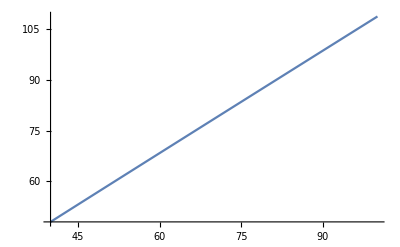

Syntax::bktmop: Expression "x-Log[Trh[x]/M],{x,40,100}]" has no opening "[".

```mathematica
Plot[x-Log[Trh[x]],{x,40,100}]
```

```mathematica
NSolve[x==Log[Trh[x]]+68, x]
```

{{x→62.3326}}

```mathematica
fff[62.3326]
```

70.6935

```mathematica
fff[x_] := Re[x-Log[Trh[x]] ]
fff[59.67]
fff[63.0289]
fff[62.3326]
```

67.9987

71.398

70.6935

```mathematica
NSolve[fff[x] - 68==0, x]
```

NSolve::fulldim: The solution set contains a full-dimensional component; use Reduce for complete solution information.

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{}}

```mathematica
Flatten[{{}}]
```

{}

```mathematica
FindRoot[fff[x]==68,{x,60}]
```

{x→62.3326}

```mathematica
fff[63.0177]
```

71.3341

```mathematica
62.3326-59.67
```

2.6626

```mathematica
Reduce[fff[x]==68,{x}]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Re[x]==62.3326

```mathematica
Solve[Re[x]==62.33264662641329,{x}]
```

Solve::fulldim: The solution set contains a full-dimensional component; use Reduce for complete solution information.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{}}

```mathematica
TRH[N_]:=((3 δ^2)/(8(N+1)^3))^(1/4)
```

```mathematica
ff[x_]:=x-Log[TRH[x]]
```

```mathematica
x/.FindRoot[ff[x]==68,{x,60}]
```

59.6713